# Regression {λ, L} Synoptic Plots

Anil Radhakrishnan, John F. Lindner, Scott T. Miller, Sudeshna Sinha, William L. Ditto, 
"Growing Neural Networks: Dynamic Evolution through Gradient Descent" 
for Figures 6 & 7.

## Preamble

```mathematica
$Version
```

14.1.0 for Mac OS X ARM (64-bit) (July 16, 2024)

```mathematica
Clear["Global`*"]
```

## Data

```mathematica
λL0L5sLogE3p0=;
```

```mathematica
λL0L5sLogE3p25=;
```

```mathematica
λL0L5sLogE3p5=;
```

```mathematica
λL0L5sLogE3p75=;
```

```mathematica
λL0L5sLogE4p0=;
```

```mathematica
λL0L5sLogE4p25=;
```

```mathematica
λL0L5sLogE4p5=;
```

```mathematica
λL0L5sLogE4p75=;
```

```mathematica
λL0L5sLogEs={λL0L5sLogE3p0,λL0L5sLogE3p25,λL0L5sLogE3p5,λL0L5sLogE3p75,λL0L5sLogE4p0,λL0L5sLogE4p25,λL0L5sLogE4p5};
```

```mathematica
nRuns=Length@λL0L5sLogEs
```

7

```mathematica
{10^3,10^3.25,10^3.5,10^3.75,10^4,10^4.25,10^4.5,10^5}
```

{1000,1778.28,3162.28,5623.41,10000,17782.8,31622.8,100000}

## Raw & Mean Plots

```mathematica
average[data_,rad_]:=Transpose[{data[[Round[(rad+1)/2]-1;;Length@data-Round[(rad-1)/2]-1,1]],MovingAverage[data[[All,2]],rad]}]
```

```mathematica
plot[data_,spread_,h_,b_]:=Module[{λRs},
λLs={#[[1]],#[[2,1]]}&/@data;
Show[
ListLogLogPlot[λLs
,PlotRange->{{0.0085,120},{0.001,10}}
,Joined->False
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["L_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Hue[h,0.5,b,0.7]
,ImageSize->500
(*,GridLines->{None,{1}}
,GridLinesStyle->Directive[Red,Thick, Dashed]*)
],
ListLogLogPlot[average[λLs,spread],Joined->True,PlotStyle->Directive[Thickness[0.007],Hue[h,1,b,0.7]]]
]
]
```

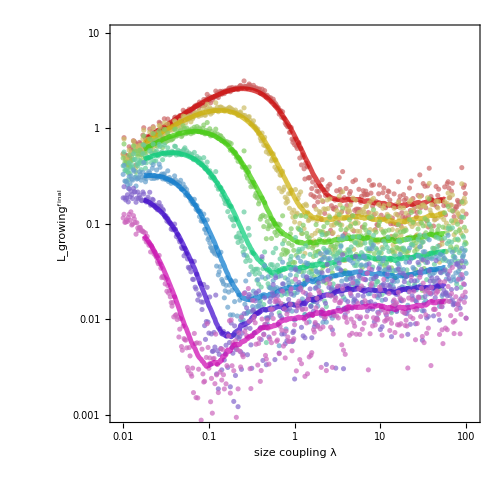

```mathematica
Show@MapIndexed[plot[#1,50,(#2[[1]]-1)/nRuns,0.8]&,λL0L5sLogEs]
```

## Mean Log Plots {λ,E}

```mathematica
meanPlot1[data_,spread_,h_,b_]:=Module[{λRs},
λLs={#[[1]],#[[2,1]]}&/@data;
ListLogLogPlot[average[λLs,spread]
,Joined->True
,PlotRange->{{0.0085,120},{0.001,10}}
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling λ",Rotate["L_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Directive[Thickness[0.007],Hue[h,1,b,0.7]]
,ImageSize->500
]
]
```

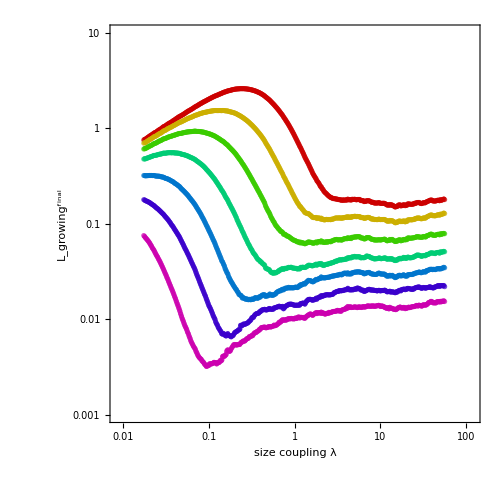

```mathematica
Show@MapIndexed[meanPlot1[#1,50,(#2[[1]]-1)/nRuns,0.8]&,λL0L5sLogEs]
```

## Mean Linear Plots {log_10 λ,log_10 E}

```mathematica
meanPlot[data_,spread_,h_,b_]:=Module[{λLs},
λLs={Log10[#[[1]]],Log10[#[[2,1]]]}&/@data;
ListPlot[average[λLs,spread]
,Joined->True
,PlotRange->{{-2,2},{-3,1}}
,Mesh->All
,AspectRatio->1
,Frame->True
,FrameLabel->{"size coupling log_10λ",Rotate["log_10L_growing^final",-90°]}
,FrameTicksStyle->18
,FrameStyle->24
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotStyle->Directive[Thickness[0.007],Hue[h,1,b,0.7]]
,ImageSize->700
]
]
```

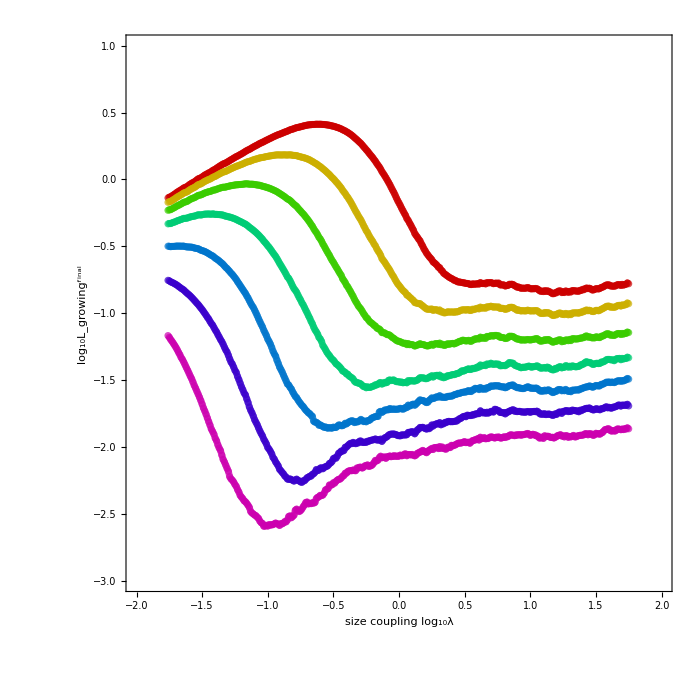

```mathematica
Show@MapIndexed[meanPlot[#1,50,(#2[[1]]-1)/nRuns,0.8]&,λL0L5sLogEs]
```

## Interpolated {λ,E,L}

```mathematica
rawlogEloglλlogR=Table[
{3+0.25(n-1),Log10[#[[1]]],Log10[#[[2,1]]]}&/@λL0L5sLogEs[[n]],
{n,1,nRuns}];
```

```mathematica
ListPointPlot3D[rawlogEloglλlogR,BoxRatios->{1, 1, 1},AxesLabel->{"log_10λ","log_10E","log_10L"},AxesStyle->16,TicksStyle->11]
```

-Graphics3D-

```mathematica
logEloglλlogR=Table[
{#[[1]],3+0.25(n-1),#[[2]]}&/@average[{Log10[#[[1]]],Log10[#[[2,1]]]}&/@λL0L5sLogEs[[n]],50],
{n,1,nRuns}];
```

```mathematica
ListPointPlot3D[logEloglλlogR,BoxRatios->{1, 1, 1},AxesLabel->{"log_10λ","log_10E","log_10L"},AxesStyle->16,TicksStyle->11]
```

-Graphics3D-

```mathematica
logEloglλlogRFlat=logEloglλlogR//Flatten[#,1]&;
```

```mathematica
rwb[z_]:=If[z<0,Hue[0,-z,1],Hue[2/3,z,1]]
```

```mathematica
ListPlot3D[logEloglλlogRFlat,PlotRange->{{-2,2},{3.0,4.5},All},BoxRatios->{1, 1, 1},MeshFunctions->{#3&},AxesLabel->{"log_10λ","log_10E","log_10L"},AxesStyle->16,TicksStyle->11]
```

-Graphics3D-

```mathematica
ListPlot3D[logEloglλlogRFlat,BoxRatios->{1, 1, 1},PlotRange->{{-2,2},{3.0,4.5},All},MeshFunctions->{#3&},ColorFunction->"LightTerrain",ColorFunctionScaling->True,InterpolationOrder->3,AxesLabel->{"log_10λ","log_10E","log_10L"},LabelStyle->{FontFamily->"CMU Serif",Black},AxesStyle->16,TicksStyle->11,ImageSize->400,ScalingFunctions->{"Reverse",Identity,Identity}]
```

-Graphics3D-

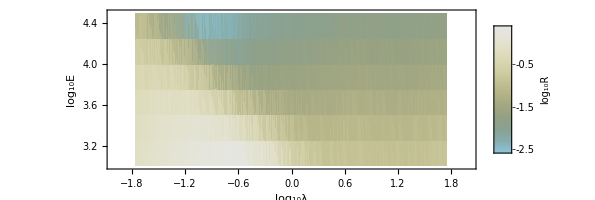

```mathematica
ListDensityPlot[logEloglλlogRFlat,PlotRange->{{-2,2},{3,4.5},All},BoxRatios->{1, 1, 1},MeshFunctions->{#3&},InterpolationOrder->3,ColorFunction->"LightTerrain",ColorFunctionScaling->True,FrameLabel->{"log_10λ","log_10E"},RotateLabel->False,PlotLegends->BarLegend[Automatic,LegendMarkerSize->130,LegendLabel->"log_10L"],FrameTicksStyle->12,FrameStyle->18,LabelStyle->{FontFamily->"CMU Serif",Black},PlotRangePadding->None,AspectRatio->Automatic,ImageSize->500]
```

```mathematica
Ε[λ_]:=10^(10/3)λ^(-5/6) (* approx fit to linear feature *)
```

```mathematica
Ε[10^0.4]
```

1000.

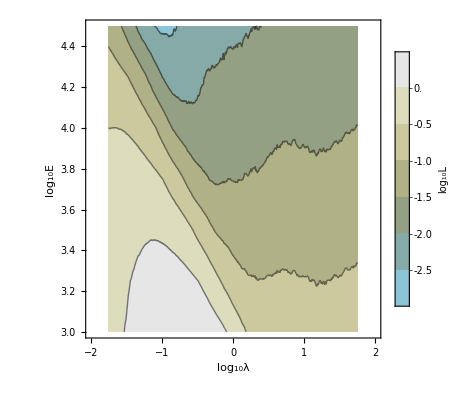

```mathematica
lPlot=ListContourPlot[logEloglλlogRFlat,PlotRange->{{-2,2},{3.0,4.5},All},BoxRatios->{1, 1, 1},MeshFunctions->{#3&},InterpolationOrder->1,
ColorFunction->"LightTerrain",ColorFunctionScaling->True,FrameLabel->{"log_10λ","log_10E"},RotateLabel->False,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10L"],FrameTicksStyle->12
,FrameStyle->18,LabelStyle->{FontFamily->"CMU Serif",Black},PlotRangePadding->None]
```

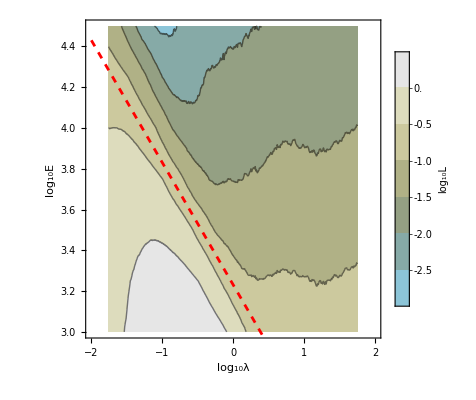

```mathematica
fitPlot=Plot[Log10[1700]-0.6logλ,{logλ,-2,2},PlotStyle->Directive[Red,Dashed]];
Show[lPlot,fitPlot]
```

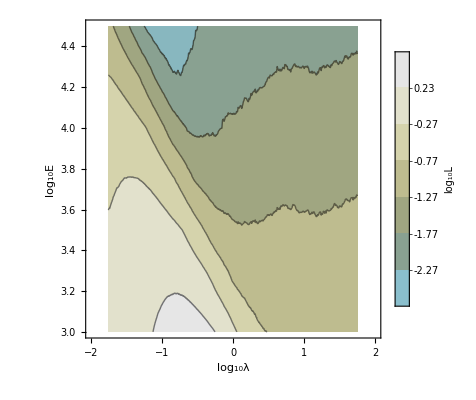

```mathematica
lPlot=ListContourPlot[logEloglλlogRFlat
,PlotRange->{{-2,2},{3.0,4.5},All}
,Contours->Range[-2.5,1,0.5]-0.77
,MeshFunctions->{#3&}
,InterpolationOrder->2
,ColorFunction->"LightTerrain"
,ColorFunctionScaling->True
,FrameLabel->{"log_10λ","log_10E"}
,RotateLabel->False
,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10L"]
,FrameTicksStyle->12
,FrameStyle->18
,LabelStyle->{FontFamily->"CMU Serif",Black}
,PlotRangePadding->None
]
```